### Differential Equations Example

```mathematica
de=m*x''[t]==-k*x[t]
```

2 x''[t]==-3 x[t]

```mathematica
sol=DSolveValue[{de,x[0]==10,x'[0]==0},{x[t]},{t}]
```

{10 Cos[√(3/2) t]}

```mathematica
m=2
```

2

```mathematica
k=3
```

3

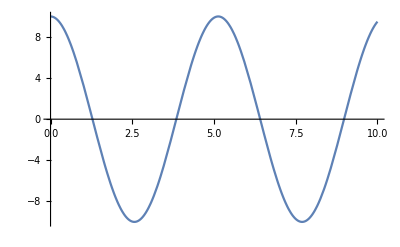

```mathematica
Plot[sol,{t,0,10}]
```